```mathematica
hao
```

```mathematica
<<MaTeX`
SetDirectory["/Users/Apple/Documents/LaTeX&Mathematica"];
```

The MaTeX configuration was corrupted so it had to be re-set. If you can reproduce this problem, please go to https://github.com/szhorvat/MaTeX and create a bug report.

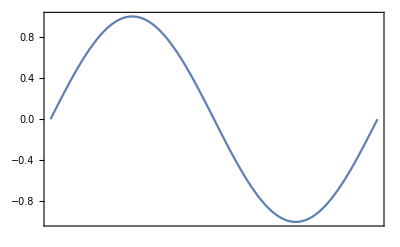

```mathematica
Plot[Sin[x],{x,0,2 Pi},Frame->True,FrameStyle->BlackFrame,FrameTicks->{{Automatic,None},{With[{ticks=Pi/4 Range[0,8]},Thread[{ticks,MaTeX[ticks,"DisplayStyle"->False]}]],None}},FrameLabel->MaTeX@{"x","\\sin x"},BaseStyle->texStyle]
```

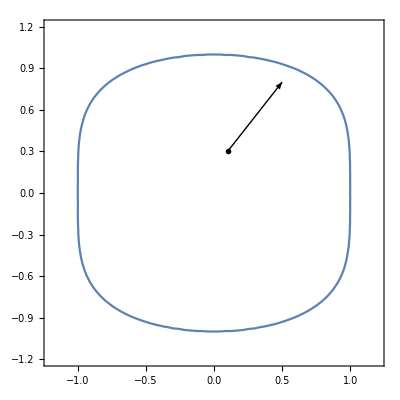

```mathematica
texStyle={FontFamily->"Latin Modern Roman",FontSize->12};
ContourPlot[x^2+y^4==1,{x,-1.2,1.2},{y,-1.2,1.2},BaseStyle->texStyle,Epilog->{Arrow[{{0.1,0.3},{0.5,0.80}}],Inset[MaTeX["x^2+y^4=1",Magnification->2],{0.1,0.3},Scaled[{0.5,1}]]}]
```

```mathematica
SetDirectory["/Users/Apple/Documents/LaTeX&Mathematica"];
Export["speedplot.eps",Plot[4Pi*(M/(2Pi*R*T))^(3/2)*v^2*Exp[(-M*v^2)/(2Pi*R*T)]/.{M->0.029,R->8.314,T->200},{v,0,2600},AxesLabel->MaTeX/@{"v/(m s^{-1})",c},PlotStyle->Black]]
```

speedplot.eps

```mathematica
NDSolve[{D[cA1[t],t]==-ka/V1*If[cA1[t]>=cA2[t],cA1[t]-cA2[t],0],
	D[cB1[t],t]==kb/V1*If[cB2[t]>=cB1[t],cB2[t]-cB1[t],0],
	D[cA2[t],t]==ka/V2*If[cA1[t]>=cA2[t],cA1[t]-cA2[t],0]-k1*cA2[t]+k2*cB2[t],
	D[cB2[t],t]==-kb/V2*If[cB2[t]>=cB1[t],cB2[t]-cB1[t],0]+k1*cA2[t]-k2*cB2[t],
	cA1[0]==0,cB1[0]==c,cA2[0]==0,cB2[0]==0}/.{ka->10,kb->10,k1->1,k2->1,c->1,V1->1,V2->0.001},
{cA1[t],cB1[t],cA2[t],cB2[t]},{t,0,1000}];
Export["antireaction.eps",LogLinearPlot[Evaluate[{cA1[t],cB1[t],cA2[t],cB2[t]}/.%],{t,0,1000},AxesLabel->{t,c},PlotLegends->{cA1[t],cB1[t],cA2[t],cB2[t]},ImageSize->Large]]
```

antireaction.eps

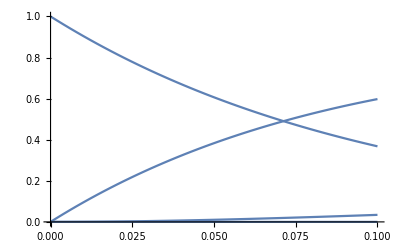

```mathematica
Plot[{cA1[t],cB1[t],cA2[t],cB2[t]}/.%17,{t,0,0.1}]
```

```mathematica
Simplify@%
```

{{cA1[t]→c ⅇ^(-ka t),cA2[t]→(c ⅇ^(-ka t) ((-1+ⅇ^(ka t)) k2 (k2-ka)+k1 ((-1+ⅇ^(ka t)) k2+ka-ⅇ^(-(k1+k2-ka) t) ka)))/((k1+k2) (k1+k2-ka)),cB1[t]→0,cB2[t]→(c ⅇ^(-(k1+k2) t) k1 (-ⅇ^((k1+k2-ka) t) (k1+k2)+ⅇ^((k1+k2) t) (k1+k2-ka)+ka))/((k1+k2) (k1+k2-ka))}}

```mathematica
DSolve[{D[cA1[t],t]==-ka/V1*(cA1[t]-cA2[t]),
	D[cB1[t],t]==kb/V1*(cB2[t]-cB1[t]),
	D[cA2[t],t]==ka/V2*(cA1[t]-cA2[t])-k1*cA2[t]+k2*cB2[t],
	D[cB2[t],t]==-kb/V2*(cB2[t]-cB1[t])+k1*cA2[t]-k2*cB2[t],
	cA1[0]==c,cB1[0]==0,cA2[0]==0,cB2[0]==0}/.{ka->10,kb->10,k1->1,k2->1,c->1,V1->1,V2->0.001},
{cA1[t],cB1[t],cA2[t],cB2[t]},t];
Export["reaction.eps",LogLinearPlot[Evaluate[{cA1[t],cB1[t],cA2[t],cB2[t]}/.%],{t,0,1000},AxesLabel->{t,c},PlotLabels->(Style[#,15]&/@{cA1[t],cB1[t],cA2[t],cB2[t]}),ImageSize->Large]]
```

reaction.eps

```mathematica
DSolve[{D[cA1[t],t]==-ka/V1*(cA1[t]-cA2[t]),
	D[cB1[t],t]==kb/V1*(cB2[t]-cB1[t]),
	D[cA2[t],t]==ka/V2*(cA1[t]-cA2[t])-k1*cA2[t]+k2*cB2[t],
	D[cB2[t],t]==-kb/V2*(cB2[t]-cB1[t])+k1*cA2[t]-k2*cB2[t],
	cA1[0]==c,cB1[0]==0,cA2[0]==0,cB2[0]==0}/.{ka->10,kb->10,k1->10,k2->10,c->1,V1->1,V2->0.1},
{cA1[t],cB1[t],cA2[t],cB2[t]},t];
Plot[Evaluate[{cA1[t],cB1[t],cA2[t],cB2[t]}/.%],{t,0,10},AxesLabel->{t,c},PlotLegends->{cA1[t],cB1[t],cA2[t],cB2[t]},ImageSize->Large]
```

{{cA1[t]→0.454545 ⅇ^(-240. t) (0.0731932 ⅇ^(111.557 t)+0.1 ⅇ^(130. t)+1.02681 ⅇ^(238.443 t)+1. ⅇ^(240. t)),cA2[t]→0.454545 ⅇ^(-240. t) (-0.866921 ⅇ^(111.557 t)-1. ⅇ^(130. t)+0.866921 ⅇ^(238.443 t)+1. ⅇ^(240. t)),cB1[t]→0.454545 ⅇ^(-240. t) (-0.0731932 ⅇ^(111.557 t)+0.1 ⅇ^(130. t)-1.02681 ⅇ^(238.443 t)+1. ⅇ^(240. t)),cB2[t]→0.454545 ⅇ^(-240. t) (0.866921 ⅇ^(111.557 t)-1. ⅇ^(130. t)-0.866921 ⅇ^(238.443 t)+1. ⅇ^(240. t))}}

reaction1.eps

```mathematica
Clear[f];
```

```mathematica
list={{-kA/V1,kA/V1,0,0},{kA/V2,-kA/V2-k1,k2,0},{0,k1,-k2-kB/V2,kB/V2},{0,0,kB/V1,-kB/V1}};
list1=Transpose@(Eigenvectors@list);
list2=Inverse[list1];
A=list2.list.list1//Simplify;
temporarylist=FullSimplify@Flatten[Array[f[#,x]&,4]/.DSolve[(list2.list.list1//Simplify).Array[f[#,x]&,4]==D[Array[f[#,x]&,4],x],Array[f[#,x]&,4],x]];
functionlist=FullSimplify@(list1.temporarylist.list2);
constantlist=FullSimplify@Solve[(functionlist/.x->0)=={c,0,0,0},Array[C,4]];
function=FullSimplify@(functionlist/.constantlist)
```

{{0,0,0,0},{0,(-k1 kA kB V1^2 V2^2-k2 kA kB V1^2 V2^2-k1 kA kB V1 V2^3-k2 kA kB V1 V2^3-4 (k1+k2) kA kB V1 V2^2 (V1+V2)-((k1+k2) V1 V2+kA (V1+V2)+kB (V1+V2))^3+4 ((k1+k2) V1 V2+kA (V1+V2)+kB (V1+V2)) (kB V1 V2 (k2 V2+k1 (V1+V2))+kA (kB (V1+V2)^2+V1 V2 (k1 V2+k2 (V1+V2))))+(kB V1 V2 (k2 V2+k1 (V1+V2))+kA (kB (V1+V2)^2+V1 V2 (k1 V2+k2 (V1+V2)))) Root[k1 kA kB V1^2 V2^2+k2 kA kB V1^2 V2^2+k1 kA kB V1 V2^3+k2 kA kB V1 V2^3+(kA kB V1^2+2 kA kB V1 V2+k2 kA V1^2 V2+k1 kB V1^2 V2+kA kB V2^2+k1 kA V1 V2^2+k2 kA V1 V2^2+k1 kB V1 V2^2+k2 kB V1 V2^2) #1+(kA V1+kB V1+kA V2+kB V2+k1 V1 V2+k2 V1 V2) #1^2+#1^3&,2]+((k1+k2) V1 V2+kA (V1+V2)+kB (V1+V2)) Root[k1 kA kB V1^2 V2^2+k2 kA kB V1^2 V2^2+k1 kA kB V1 V2^3+k2 kA kB V1 V2^3+(kA kB V1^2+2 kA kB V1 V2+k2 kA V1^2 V2+k1 kB V1^2 V2+kA kB V2^2+k1 kA V1 V2^2+k2 kA V1 V2^2+k1 kB V1 V2^2+k2 kB V1 V2^2) #1+(kA V1+kB V1+kA V2+kB V2+k1 V1 V2+k2 V1 V2) #1^2+#1^3&,2]^2+Root[k1 kA kB V1^2 V2^2+k2 kA kB V1^2 V2^2+k1 kA kB V1 V2^3+k2 kA kB V1 V2^3+(kA kB V1^2+2 kA kB V1 V2+k2 kA V1^2 V2+k1 kB V1^2 V2+kA kB V2^2+k1 kA V1 V2^2+k2 kA V1 V2^2+k1 kB V1 V2^2+k2 kB V1 V2^2) #1+(kA V1+kB V1+kA V2+kB V2+k1 V1 V2+k2 V1 V2) #1^2+#1^3&,1] Root[k1 kA kB V1^2 V2^2+k2 kA kB V1^2 V2^2+k1 kA kB V1 V2^3+k2 kA kB V1 V2^3+(kA kB V1^2+2 kA kB V1 V2+k2 kA V1^2 V2+k1 kB V1^2 V2+kA kB V2^2+k1 kA V1 V2^2+k2 kA V1 V2^2+k1 kB V1 V2^2+k2 kB V1 V2^2) #1+(kA V1+kB V1+kA V2+kB V2+k1 V1 V2+k2 V1 V2) #1^2+#1^3&,2]^2+(kB V1 V2 (k2 V2+k1 (V1+V2))+kA (kB (V1+V2)^2+V1 V2 (k1 V2+k2 (V1+V2)))) Root[k1 kA kB V1^2 V2^2+k2 kA kB V1^2 V2^2+k1 kA kB V1 V2^3+k2 kA kB V1 V2^3+(kA kB V1^2+2 kA kB V1 V2+k2 kA V1^2 V2+k1 kB V1^2 V2+kA kB V2^2+k1 kA V1 V2^2+k2 kA V1 V2^2+k1 kB V1 V2^2+k2 kB V1 V2^2) #1+(kA V1+kB V1+kA V2+kB V2+k1 V1 V2+k2 V1 V2) #1^2+#1^3&,3]+Root[k1 kA kB V1^2 V2^2+k2 kA kB V1^2 V2^2+k1 kA kB V1 V2^3+k2 kA kB V1 V2^3+(kA kB V1^2+2 kA kB V1 V2+k2 kA V1^2 V2+k1 kB V1^2 V2+kA kB V2^2+k1 kA V1 V2^2+k2 kA V1 V2^2+k1 kB V1 V2^2+k2 kB V1 V2^2) #1+(kA V1+kB V1+kA V2+kB V2+k1 V1 V2+k2 V1 V2) #1^2+#1^3&,2]^2 Root[k1 kA kB V1^2 V2^2+k2 kA kB V1^2 V2^2+k1 kA kB V1 V2^3+k2 kA kB V1 V2^3+(kA kB V1^2+2 kA kB V1 V2+k2 kA V1^2 V2+k1 kB V1^2 V2+kA kB V2^2+k1 kA V1 V2^2+k2 kA V1 V2^2+k1 kB V1 V2^2+k2 kB V1 V2^2) #1+(kA V1+kB V1+kA V2+kB V2+k1 V1 V2+k2 V1 V2) #1^2+#1^3&,3]+((k1+k2) V1 V2+kA (V1+V2)+kB (V1+V2)) Root[k1 kA kB V1^2 V2^2+k2 kA kB V1^2 V2^2+k1 kA kB V1 V2^3+k2 kA kB V1 V2^3+(kA kB V1^2+2 kA kB V1 V2+k2 kA V1^2 V2+k1 kB V1^2 V2+kA kB V2^2+k1 kA V1 V2^2+k2 kA V1 V2^2+k1 kB V1 V2^2+k2 kB V1 V2^2) #1+(kA V1+kB V1+kA V2+kB V2+k1 V1 V2+k2 V1 V2) #1^2+#1^3&,3]^2+Root[k1 kA kB V1^2 V2^2+k2 kA kB V1^2 V2^2+k1 kA kB V1 V2^3+k2 kA kB V1 V2^3+(kA kB V1^2+2 kA kB V1 V2+k2 kA V1^2 V2+k1 kB V1^2 V2+kA kB V2^2+k1 kA V1 V2^2+k2 kA V1 V2^2+k1 kB V1 V2^2+k2 kB V1 V2^2) #1+(kA V1+kB V1+kA V2+kB V2+k1 V1 V2+k2 V1 V2) #1^2+#1^3&,1] Root[k1 kA kB V1^2 V2^2+k2 kA kB V1^2 V2^2+k1 kA kB V1 V2^3+k2 kA kB V1 V2^3+(kA kB V1^2+2 kA kB V1 V2+k2 kA V1^2 V2+k1 kB V1^2 V2+kA kB V2^2+k1 kA V1 V2^2+k2 kA V1 V2^2+k1 kB V1 V2^2+k2 kB V1 V2^2) #1+(kA V1+kB V1+kA V2+kB V2+k1 V1 V2+k2 V1 V2) #1^2+#1^3&,3]^2+Root[k1 kA kB V1^2 V2^2+k2 kA kB V1^2 V2^2+k1 kA kB V1 V2^3+k2 kA kB V1 V2^3+(kA kB V1^2+2 kA kB V1 V2+k2 kA V1^2 V2+k1 kB V1^2 V2+kA kB V2^2+k1 kA V1 V2^2+k2 kA V1 V2^2+k1 kB V1 V2^2+k2 kB V1 V2^2) #1+(kA V1+kB V1+kA V2+kB V2+k1 V1 V2+k2 V1 V2) #1^2+#1^3&,2] Root[k1 kA kB V1^2 V2^2+k2 kA kB V1^2 V2^2+k1 kA kB V1 V2^3+k2 kA kB V1 V2^3+(kA kB V1^2+2 kA kB V1 V2+k2 kA V1^2 V2+k1 kB V1^2 V2+kA kB V2^2+k1 kA V1 V2^2+k2 kA V1 V2^2+k1 kB V1 V2^2+k2 kB V1 V2^2) #1+(kA V1+kB V1+kA V2+kB V2+k1 V1 V2+k2 V1 V2) #1^2+#1^3&,3]^2)/(V1 V2 (Root[k1 kA kB V1^2 V2^2+k2 kA kB V1^2 V2^2+k1 kA kB V1 V2^3+k2 kA kB V1 V2^3+(kA kB V1^2+2 kA kB V1 V2+k2 kA V1^2 V2+k1 kB V1^2 V2+kA kB V2^2+k1 kA V1 V2^2+k2 kA V1 V2^2+k1 kB V1 V2^2+k2 kB V1 V2^2) #1+(kA V1+kB V1+kA V2+kB V2+k1 V1 V2+k2 V1 V2) #1^2+#1^3&,1]-Root[k1 kA kB V1^2 V2^2+k2 kA kB V1^2 V2^2+k1 kA kB V1 V2^3+k2 kA kB V1 V2^3+(kA kB V1^2+2 kA kB V1 V2+k2 kA V1^2 V2+k1 kB V1^2 V2+kA kB V2^2+k1 kA V1 V2^2+k2 kA V1 V2^2+k1 kB V1 V2^2+k2 kB V1 V2^2) #1+(kA V1+kB V1+kA V2+kB V2+k1 V1 V2+k2 V1 V2) #1^2+#1^3&,2]) (Root[k1 kA kB V1^2 V2^2+k2 kA kB V1^2 V2^2+k1 kA kB V1 V2^3+k2 kA kB V1 V2^3+(kA kB V1^2+2 kA kB V1 V2+k2 kA V1^2 V2+k1 kB V1^2 V2+kA kB V2^2+k1 kA V1 V2^2+k2 kA V1 V2^2+k1 kB V1 V2^2+k2 kB V1 V2^2) #1+(kA V1+kB V1+kA V2+kB V2+k1 V1 V2+k2 V1 V2) #1^2+#1^3&,1]-Root[k1 kA kB V1^2 V2^2+k2 kA kB V1^2 V2^2+k1 kA kB V1 V2^3+k2 kA kB V1 V2^3+(kA kB V1^2+2 kA kB V1 V2+k2 kA V1^2 V2+k1 kB V1^2 V2+kA kB V2^2+k1 kA V1 V2^2+k2 kA V1 V2^2+k1 kB V1 V2^2+k2 kB V1 V2^2) #1+(kA V1+kB V1+kA V2+kB V2+k1 V1 V2+k2 V1 V2) #1^2+#1^3&,3])),0,0},{0,0,(2 k1 kA kB V1^2 V2^2+2 k2 kA kB V1^2 V2^2+2 k1 kA kB V1 V2^3+2 k2 kA kB V1 V2^3+(kB V1 V2 (k2 V2+k1 (V1+V2))+kA (kB (V1+V2)^2+V1 V2 (k1 V2+k2 (V1+V2)))) Root[k1 kA kB V1^2 V2^2+k2 kA kB V1^2 V2^2+k1 kA kB V1 V2^3+k2 kA kB V1 V2^3+(kA kB V1^2+2 kA kB V1 V2+k2 kA V1^2 V2+k1 kB V1^2 V2+kA kB V2^2+k1 kA V1 V2^2+k2 kA V1 V2^2+k1 kB V1 V2^2+k2 kB V1 V2^2) #1+(kA V1+kB V1+kA V2+kB V2+k1 V1 V2+k2 V1 V2) #1^2+#1^3&,2]+((k1+k2) V1 V2+kA (V1+V2)+kB (V1+V2)) Root[k1 kA kB V1^2 V2^2+k2 kA kB V1^2 V2^2+k1 kA kB V1 V2^3+k2 kA kB V1 V2^3+(kA kB V1^2+2 kA kB V1 V2+k2 kA V1^2 V2+k1 kB V1^2 V2+kA kB V2^2+k1 kA V1 V2^2+k2 kA V1 V2^2+k1 kB V1 V2^2+k2 kB V1 V2^2) #1+(kA V1+kB V1+kA V2+kB V2+k1 V1 V2+k2 V1 V2) #1^2+#1^3&,2]^2+Root[k1 kA kB V1^2 V2^2+k2 kA kB V1^2 V2^2+k1 kA kB V1 V2^3+k2 kA kB V1 V2^3+(kA kB V1^2+2 kA kB V1 V2+k2 kA V1^2 V2+k1 kB V1^2 V2+kA kB V2^2+k1 kA V1 V2^2+k2 kA V1 V2^2+k1 kB V1 V2^2+k2 kB V1 V2^2) #1+(kA V1+kB V1+kA V2+kB V2+k1 V1 V2+k2 V1 V2) #1^2+#1^3&,1] Root[k1 kA kB V1^2 V2^2+k2 kA kB V1^2 V2^2+k1 kA kB V1 V2^3+k2 kA kB V1 V2^3+(kA kB V1^2+2 kA kB V1 V2+k2 kA V1^2 V2+k1 kB V1^2 V2+kA kB V2^2+k1 kA V1 V2^2+k2 kA V1 V2^2+k1 kB V1 V2^2+k2 kB V1 V2^2) #1+(kA V1+kB V1+kA V2+kB V2+k1 V1 V2+k2 V1 V2) #1^2+#1^3&,2]^2+Root[k1 kA kB V1^2 V2^2+k2 kA kB V1^2 V2^2+k1 kA kB V1 V2^3+k2 kA kB V1 V2^3+(kA kB V1^2+2 kA kB V1 V2+k2 kA V1^2 V2+k1 kB V1^2 V2+kA kB V2^2+k1 kA V1 V2^2+k2 kA V1 V2^2+k1 kB V1 V2^2+k2 kB V1 V2^2) #1+(kA V1+kB V1+kA V2+kB V2+k1 V1 V2+k2 V1 V2) #1^2+#1^3&,2]^2 Root[k1 kA kB V1^2 V2^2+k2 kA kB V1^2 V2^2+k1 kA kB V1 V2^3+k2 kA kB V1 V2^3+(kA kB V1^2+2 kA kB V1 V2+k2 kA V1^2 V2+k1 kB V1^2 V2+kA kB V2^2+k1 kA V1 V2^2+k2 kA V1 V2^2+k1 kB V1 V2^2+k2 kB V1 V2^2) #1+(kA V1+kB V1+kA V2+kB V2+k1 V1 V2+k2 V1 V2) #1^2+#1^3&,3])/(V1 V2 (kA kB V1^2+2 kA kB V1 V2+k2 kA V1^2 V2+k1 kB V1^2 V2+kA kB V2^2+k1 kA V1 V2^2+k2 kA V1 V2^2+k1 kB V1 V2^2+k2 kB V1 V2^2-Root[k1 kA kB V1^2 V2^2+k2 kA kB V1^2 V2^2+k1 kA kB V1 V2^3+k2 kA kB V1 V2^3+(kA kB V1^2+2 kA kB V1 V2+k2 kA V1^2 V2+k1 kB V1^2 V2+kA kB V2^2+k1 kA V1 V2^2+k2 kA V1 V2^2+k1 kB V1 V2^2+k2 kB V1 V2^2) #1+(kA V1+kB V1+kA V2+kB V2+k1 V1 V2+k2 V1 V2) #1^2+#1^3&,2]^2-2 Root[k1 kA kB V1^2 V2^2+k2 kA kB V1^2 V2^2+k1 kA kB V1 V2^3+k2 kA kB V1 V2^3+(kA kB V1^2+2 kA kB V1 V2+k2 kA V1^2 V2+k1 kB V1^2 V2+kA kB V2^2+k1 kA V1 V2^2+k2 kA V1 V2^2+k1 kB V1 V2^2+k2 kB V1 V2^2) #1+(kA V1+kB V1+kA V2+kB V2+k1 V1 V2+k2 V1 V2) #1^2+#1^3&,1] Root[k1 kA kB V1^2 V2^2+k2 kA kB V1^2 V2^2+k1 kA kB V1 V2^3+k2 kA kB V1 V2^3+(kA kB V1^2+2 kA kB V1 V2+k2 kA V1^2 V2+k1 kB V1^2 V2+kA kB V2^2+k1 kA V1 V2^2+k2 kA V1 V2^2+k1 kB V1 V2^2+k2 kB V1 V2^2) #1+(kA V1+kB V1+kA V2+kB V2+k1 V1 V2+k2 V1 V2) #1^2+#1^3&,3])),0},{0,0,0,(2 k1 kA kB V1^2 V2^2+2 k2 kA kB V1^2 V2^2+2 k1 kA kB V1 V2^3+2 k2 kA kB V1 V2^3+(kB V1 V2 (k2 V2+k1 (V1+V2))+kA (kB (V1+V2)^2+V1 V2 (k1 V2+k2 (V1+V2)))) Root[k1 kA kB V1^2 V2^2+k2 kA kB V1^2 V2^2+k1 kA kB V1 V2^3+k2 kA kB V1 V2^3+(kA kB V1^2+2 kA kB V1 V2+k2 kA V1^2 V2+k1 kB V1^2 V2+kA kB V2^2+k1 kA V1 V2^2+k2 kA V1 V2^2+k1 kB V1 V2^2+k2 kB V1 V2^2) #1+(kA V1+kB V1+kA V2+kB V2+k1 V1 V2+k2 V1 V2) #1^2+#1^3&,3]+((k1+k2) V1 V2+kA (V1+V2)+kB (V1+V2)) Root[k1 kA kB V1^2 V2^2+k2 kA kB V1^2 V2^2+k1 kA kB V1 V2^3+k2 kA kB V1 V2^3+(kA kB V1^2+2 kA kB V1 V2+k2 kA V1^2 V2+k1 kB V1^2 V2+kA kB V2^2+k1 kA V1 V2^2+k2 kA V1 V2^2+k1 kB V1 V2^2+k2 kB V1 V2^2) #1+(kA V1+kB V1+kA V2+kB V2+k1 V1 V2+k2 V1 V2) #1^2+#1^3&,3]^2+Root[k1 kA kB V1^2 V2^2+k2 kA kB V1^2 V2^2+k1 kA kB V1 V2^3+k2 kA kB V1 V2^3+(kA kB V1^2+2 kA kB V1 V2+k2 kA V1^2 V2+k1 kB V1^2 V2+kA kB V2^2+k1 kA V1 V2^2+k2 kA V1 V2^2+k1 kB V1 V2^2+k2 kB V1 V2^2) #1+(kA V1+kB V1+kA V2+kB V2+k1 V1 V2+k2 V1 V2) #1^2+#1^3&,1] Root[k1 kA kB V1^2 V2^2+k2 kA kB V1^2 V2^2+k1 kA kB V1 V2^3+k2 kA kB V1 V2^3+(kA kB V1^2+2 kA kB V1 V2+k2 kA V1^2 V2+k1 kB V1^2 V2+kA kB V2^2+k1 kA V1 V2^2+k2 kA V1 V2^2+k1 kB V1 V2^2+k2 kB V1 V2^2) #1+(kA V1+kB V1+kA V2+kB V2+k1 V1 V2+k2 V1 V2) #1^2+#1^3&,3]^2+Root[k1 kA kB V1^2 V2^2+k2 kA kB V1^2 V2^2+k1 kA kB V1 V2^3+k2 kA kB V1 V2^3+(kA kB V1^2+2 kA kB V1 V2+k2 kA V1^2 V2+k1 kB V1^2 V2+kA kB V2^2+k1 kA V1 V2^2+k2 kA V1 V2^2+k1 kB V1 V2^2+k2 kB V1 V2^2) #1+(kA V1+kB V1+kA V2+kB V2+k1 V1 V2+k2 V1 V2) #1^2+#1^3&,2] Root[k1 kA kB V1^2 V2^2+k2 kA kB V1^2 V2^2+k1 kA kB V1 V2^3+k2 kA kB V1 V2^3+(kA kB V1^2+2 kA kB V1 V2+k2 kA V1^2 V2+k1 kB V1^2 V2+kA kB V2^2+k1 kA V1 V2^2+k2 kA V1 V2^2+k1 kB V1 V2^2+k2 kB V1 V2^2) #1+(kA V1+kB V1+kA V2+kB V2+k1 V1 V2+k2 V1 V2) #1^2+#1^3&,3]^2)/(V1 V2 (Root[k1 kA kB V1^2 V2^2+k2 kA kB V1^2 V2^2+k1 kA kB V1 V2^3+k2 kA kB V1 V2^3+(kA kB V1^2+2 kA kB V1 V2+k2 kA V1^2 V2+k1 kB V1^2 V2+kA kB V2^2+k1 kA V1 V2^2+k2 kA V1 V2^2+k1 kB V1 V2^2+k2 kB V1 V2^2) #1+(kA V1+kB V1+kA V2+kB V2+k1 V1 V2+k2 V1 V2) #1^2+#1^3&,1]-Root[k1 kA kB V1^2 V2^2+k2 kA kB V1^2 V2^2+k1 kA kB V1 V2^3+k2 kA kB V1 V2^3+(kA kB V1^2+2 kA kB V1 V2+k2 kA V1^2 V2+k1 kB V1^2 V2+kA kB V2^2+k1 kA V1 V2^2+k2 kA V1 V2^2+k1 kB V1 V2^2+k2 kB V1 V2^2) #1+(kA V1+kB V1+kA V2+kB V2+k1 V1 V2+k2 V1 V2) #1^2+#1^3&,3]) (-Root[k1 kA kB V1^2 V2^2+k2 kA kB V1^2 V2^2+k1 kA kB V1 V2^3+k2 kA kB V1 V2^3+(kA kB V1^2+2 kA kB V1 V2+k2 kA V1^2 V2+k1 kB V1^2 V2+kA kB V2^2+k1 kA V1 V2^2+k2 kA V1 V2^2+k1 kB V1 V2^2+k2 kB V1 V2^2) #1+(kA V1+kB V1+kA V2+kB V2+k1 V1 V2+k2 V1 V2) #1^2+#1^3&,2]+Root[k1 kA kB V1^2 V2^2+k2 kA kB V1^2 V2^2+k1 kA kB V1 V2^3+k2 kA kB V1 V2^3+(kA kB V1^2+2 kA kB V1 V2+k2 kA V1^2 V2+k1 kB V1^2 V2+kA kB V2^2+k1 kA V1 V2^2+k2 kA V1 V2^2+k1 kB V1 V2^2+k2 kB V1 V2^2) #1+(kA V1+kB V1+kA V2+kB V2+k1 V1 V2+k2 V1 V2) #1^2+#1^3&,3]))}}

{C[1],ⅇ^((x (-kA^3 (V1+V2)^3-(kB^2 V1^2+2 kB V1 (kB+(-k1+k2) V1) V2+(kB-(k1+k2) V1)^2 V2^2) ((k1+k2) V1 V2+kB (V1+V2))+kA^2 (V1+V2) (kB (V1+V2)^2+V1 V2 (k1 (-3 V1+V2)+k2 (V1+V2)))+kA (kB^2 (V1+V2)^3+(k1+k2) kB V1 V2 (V1+V2) (2 V1+V2)+(k1+k2) V1^2 V2^2 (k1 (-3 V1+V2)+k2 (V1+V2)))+(kB V1 V2 (k2 V2+k1 (V1+V2))+kA (kB (V1+V2)^2+V1 V2 (k2 V1+(k1+k2) V2))) Root[k1 kA kB V1^2 V2^2+k2 kA kB V1^2 V2^2+k1 kA kB V1 V2^3+k2 kA kB V1 V2^3+(kA kB V1^2+2 kA kB V1 V2+k2 kA V1^2 V2+k1 kB V1^2 V2+kA kB V2^2+k1 kA V1 V2^2+k2 kA V1 V2^2+k1 kB V1 V2^2+k2 kB V1 V2^2) #1+(kA V1+kB V1+kA V2+kB V2+k1 V1 V2+k2 V1 V2) #1^2+#1^3&,2]-Root[k1 kA kB V1^2 V2^2+k2 kA kB V1^2 V2^2+k1 kA kB V1 V2^3+k2 kA kB V1 V2^3+(kA kB V1^2+2 kA kB V1 V2+k2 kA V1^2 V2+k1 kB V1^2 V2+kA kB V2^2+k1 kA V1 V2^2+k2 kA V1 V2^2+k1 kB V1 V2^2+k2 kB V1 V2^2) #1+(kA V1+kB V1+kA V2+kB V2+k1 V1 V2+k2 V1 V2) #1^2+#1^3&,2]^3+Root[k1 kA kB V1^2 V2^2+k2 kA kB V1^2 V2^2+k1 kA kB V1 V2^3+k2 kA kB V1 V2^3+(kA kB V1^2+2 kA kB V1 V2+k2 kA V1^2 V2+k1 kB V1^2 V2+kA kB V2^2+k1 kA V1 V2^2+k2 kA V1 V2^2+k1 kB V1 V2^2+k2 kB V1 V2^2) #1+(kA V1+kB V1+kA V2+kB V2+k1 V1 V2+k2 V1 V2) #1^2+#1^3&,3] (kB V1 V2 (k2 V2+k1 (V1+V2))+kA (kB (V1+V2)^2+V1 V2 (k1 V2+k2 (V1+V2)))-Root[k1 kA kB V1^2 V2^2+k2 kA kB V1^2 V2^2+k1 kA kB V1 V2^3+k2 kA kB V1 V2^3+(kA kB V1^2+2 kA kB V1 V2+k2 kA V1^2 V2+k1 kB V1^2 V2+kA kB V2^2+k1 kA V1 V2^2+k2 kA V1 V2^2+k1 kB V1 V2^2+k2 kB V1 V2^2) #1+(kA V1+kB V1+kA V2+kB V2+k1 V1 V2+k2 V1 V2) #1^2+#1^3&,3]^2)))/(V1 V2 (Root[k1 kA kB V1^2 V2^2+k2 kA kB V1^2 V2^2+k1 kA kB V1 V2^3+k2 kA kB V1 V2^3+(kA kB V1^2+2 kA kB V1 V2+k2 kA V1^2 V2+k1 kB V1^2 V2+kA kB V2^2+k1 kA V1 V2^2+k2 kA V1 V2^2+k1 kB V1 V2^2+k2 kB V1 V2^2) #1+(kA V1+kB V1+kA V2+kB V2+k1 V1 V2+k2 V1 V2) #1^2+#1^3&,1]-Root[k1 kA kB V1^2 V2^2+k2 kA kB V1^2 V2^2+k1 kA kB V1 V2^3+k2 kA kB V1 V2^3+(kA kB V1^2+2 kA kB V1 V2+k2 kA V1^2 V2+k1 kB V1^2 V2+kA kB V2^2+k1 kA V1 V2^2+k2 kA V1 V2^2+k1 kB V1 V2^2+k2 kB V1 V2^2) #1+(kA V1+kB V1+kA V2+kB V2+k1 V1 V2+k2 V1 V2) #1^2+#1^3&,2]) (Root[k1 kA kB V1^2 V2^2+k2 kA kB V1^2 V2^2+k1 kA kB V1 V2^3+k2 kA kB V1 V2^3+(kA kB V1^2+2 kA kB V1 V2+k2 kA V1^2 V2+k1 kB V1^2 V2+kA kB V2^2+k1 kA V1 V2^2+k2 kA V1 V2^2+k1 kB V1 V2^2+k2 kB V1 V2^2) #1+(kA V1+kB V1+kA V2+kB V2+k1 V1 V2+k2 V1 V2) #1^2+#1^3&,1]-Root[k1 kA kB V1^2 V2^2+k2 kA kB V1^2 V2^2+k1 kA kB V1 V2^3+k2 kA kB V1 V2^3+(kA kB V1^2+2 kA kB V1 V2+k2 kA V1^2 V2+k1 kB V1^2 V2+kA kB V2^2+k1 kA V1 V2^2+k2 kA V1 V2^2+k1 kB V1 V2^2+k2 kB V1 V2^2) #1+(kA V1+kB V1+kA V2+kB V2+k1 V1 V2+k2 V1 V2) #1^2+#1^3&,3]))) C[2],ⅇ^((x (2 (k1+k2) kA kB V1 V2^2 (V1+V2)+(kB V1 V2 (k2 V2+k1 (V1+V2))+kA (kB (V1+V2)^2+V1 V2 (k2 V1+(k1+k2) V2))) Root[k1 kA kB V1^2 V2^2+k2 kA kB V1^2 V2^2+k1 kA kB V1 V2^3+k2 kA kB V1 V2^3+(kA kB V1^2+2 kA kB V1 V2+k2 kA V1^2 V2+k1 kB V1^2 V2+kA kB V2^2+k1 kA V1 V2^2+k2 kA V1 V2^2+k1 kB V1 V2^2+k2 kB V1 V2^2) #1+(kA V1+kB V1+kA V2+kB V2+k1 V1 V2+k2 V1 V2) #1^2+#1^3&,2]-Root[k1 kA kB V1^2 V2^2+k2 kA kB V1^2 V2^2+k1 kA kB V1 V2^3+k2 kA kB V1 V2^3+(kA kB V1^2+2 kA kB V1 V2+k2 kA V1^2 V2+k1 kB V1^2 V2+kA kB V2^2+k1 kA V1 V2^2+k2 kA V1 V2^2+k1 kB V1 V2^2+k2 kB V1 V2^2) #1+(kA V1+kB V1+kA V2+kB V2+k1 V1 V2+k2 V1 V2) #1^2+#1^3&,2]^3))/(V1 V2 (kB V1 V2 (k2 V2+k1 (V1+V2))+kA (kB (V1+V2)^2+V1 V2 (k1 V2+k2 (V1+V2)))-Root[k1 kA kB V1^2 V2^2+k2 kA kB V1^2 V2^2+k1 kA kB V1 V2^3+k2 kA kB V1 V2^3+(kA kB V1^2+2 kA kB V1 V2+k2 kA V1^2 V2+k1 kB V1^2 V2+kA kB V2^2+k1 kA V1 V2^2+k2 kA V1 V2^2+k1 kB V1 V2^2+k2 kB V1 V2^2) #1+(kA V1+kB V1+kA V2+kB V2+k1 V1 V2+k2 V1 V2) #1^2+#1^3&,2]^2-2 Root[k1 kA kB V1^2 V2^2+k2 kA kB V1^2 V2^2+k1 kA kB V1 V2^3+k2 kA kB V1 V2^3+(kA kB V1^2+2 kA kB V1 V2+k2 kA V1^2 V2+k1 kB V1^2 V2+kA kB V2^2+k1 kA V1 V2^2+k2 kA V1 V2^2+k1 kB V1 V2^2+k2 kB V1 V2^2) #1+(kA V1+kB V1+kA V2+kB V2+k1 V1 V2+k2 V1 V2) #1^2+#1^3&,1] Root[k1 kA kB V1^2 V2^2+k2 kA kB V1^2 V2^2+k1 kA kB V1 V2^3+k2 kA kB V1 V2^3+(kA kB V1^2+2 kA kB V1 V2+k2 kA V1^2 V2+k1 kB V1^2 V2+kA kB V2^2+k1 kA V1 V2^2+k2 kA V1 V2^2+k1 kB V1 V2^2+k2 kB V1 V2^2) #1+(kA V1+kB V1+kA V2+kB V2+k1 V1 V2+k2 V1 V2) #1^2+#1^3&,3]))) C[3],ⅇ^((x (2 (k1+k2) kA kB V1 V2^2 (V1+V2)+(kB V1 V2 (k2 V2+k1 (V1+V2))+kA (kB (V1+V2)^2+V1 V2 (k2 V1+(k1+k2) V2))) Root[k1 kA kB V1^2 V2^2+k2 kA kB V1^2 V2^2+k1 kA kB V1 V2^3+k2 kA kB V1 V2^3+(kA kB V1^2+2 kA kB V1 V2+k2 kA V1^2 V2+k1 kB V1^2 V2+kA kB V2^2+k1 kA V1 V2^2+k2 kA V1 V2^2+k1 kB V1 V2^2+k2 kB V1 V2^2) #1+(kA V1+kB V1+kA V2+kB V2+k1 V1 V2+k2 V1 V2) #1^2+#1^3&,3]-Root[k1 kA kB V1^2 V2^2+k2 kA kB V1^2 V2^2+k1 kA kB V1 V2^3+k2 kA kB V1 V2^3+(kA kB V1^2+2 kA kB V1 V2+k2 kA V1^2 V2+k1 kB V1^2 V2+kA kB V2^2+k1 kA V1 V2^2+k2 kA V1 V2^2+k1 kB V1 V2^2+k2 kB V1 V2^2) #1+(kA V1+kB V1+kA V2+kB V2+k1 V1 V2+k2 V1 V2) #1^2+#1^3&,3]^3))/(V1 V2 (Root[k1 kA kB V1^2 V2^2+k2 kA kB V1^2 V2^2+k1 kA kB V1 V2^3+k2 kA kB V1 V2^3+(kA kB V1^2+2 kA kB V1 V2+k2 kA V1^2 V2+k1 kB V1^2 V2+kA kB V2^2+k1 kA V1 V2^2+k2 kA V1 V2^2+k1 kB V1 V2^2+k2 kB V1 V2^2) #1+(kA V1+kB V1+kA V2+kB V2+k1 V1 V2+k2 V1 V2) #1^2+#1^3&,1]-Root[k1 kA kB V1^2 V2^2+k2 kA kB V1^2 V2^2+k1 kA kB V1 V2^3+k2 kA kB V1 V2^3+(kA kB V1^2+2 kA kB V1 V2+k2 kA V1^2 V2+k1 kB V1^2 V2+kA kB V2^2+k1 kA V1 V2^2+k2 kA V1 V2^2+k1 kB V1 V2^2+k2 kB V1 V2^2) #1+(kA V1+kB V1+kA V2+kB V2+k1 V1 V2+k2 V1 V2) #1^2+#1^3&,3]) (-Root[k1 kA kB V1^2 V2^2+k2 kA kB V1^2 V2^2+k1 kA kB V1 V2^3+k2 kA kB V1 V2^3+(kA kB V1^2+2 kA kB V1 V2+k2 kA V1^2 V2+k1 kB V1^2 V2+kA kB V2^2+k1 kA V1 V2^2+k2 kA V1 V2^2+k1 kB V1 V2^2+k2 kB V1 V2^2) #1+(kA V1+kB V1+kA V2+kB V2+k1 V1 V2+k2 V1 V2) #1^2+#1^3&,2]+Root[k1 kA kB V1^2 V2^2+k2 kA kB V1^2 V2^2+k1 kA kB V1 V2^3+k2 kA kB V1 V2^3+(kA kB V1^2+2 kA kB V1 V2+k2 kA V1^2 V2+k1 kB V1^2 V2+kA kB V2^2+k1 kA V1 V2^2+k2 kA V1 V2^2+k1 kB V1 V2^2+k2 kB V1 V2^2) #1+(kA V1+kB V1+kA V2+kB V2+k1 V1 V2+k2 V1 V2) #1^2+#1^3&,3]))) C[4]}

$Aborted

{}

functionlist

```mathematica
DSolve[{D[cA1[t],t]==-ka/V1*(cA1[t]-cA2[t]),
	D[cB1[t],t]==kb/V1*(cB2[t]-cB1[t]),
	D[cA2[t],t]==ka/V2*(cA1[t]-cA2[t])-k1*cA2[t]+k2*cB2[t],
	D[cB2[t],t]==-kb/V2*(cB2[t]-cB1[t])+k1*cA2[t]-k2*cB2[t],
	cA1[0]==c,cB1[0]==0,cA2[0]==0,cB2[0]==0}/.{ka->10,kb->10,k1->2,k2->1,c->1,V1->1,V2->0.1},
{cA1[t],cB1[t],cA2[t],cB2[t]},t];
Export["reaction.eps",Plot[Evaluate[{cA1[t],cB1[t],cA2[t],cB2[t]}/.%],{t,0,15},PlotLegends->{cA1[t],cB1[t],cA2[t],cB2[t]},ImageSize->Large]]
```

reaction.eps

```mathematica
Clear[AA,Aa,aa];
AA[1]=0;
Aa[1]=0.4;
aa[1]=0.6;
AA[n_]:=(AA[n-1]^2+AA[n-1]*Aa[n-1]+1/4 Aa[n-1]^2)/(AA[n-1]+Aa[n-1]+aa[n-1])^2;
Aa[n_]:=2*(1-Aa[n-1]/(AA[n-1]+Aa[n-1]+aa[n-1]))(2*AA[n-1]*aa[n-1]+AA[n-1]*Aa[n-1]+1/2 Aa[n-1]^2)/(AA[n-1]+Aa[n-1]+aa[n-1])^2 ;
aa[n_]:=(1-aa[n-1]/(AA[n-1]+Aa[n-1]+aa[n-1]))(aa[n-1]^2+aa[n-1]*Aa[n-1]*Aa[n-1]+1/4 Aa[n-1]^2 )/(AA[n-1]+Aa[n-1]+aa[n-1])^2;
{"AA",AA[2]/(AA[2]+Aa[2]+aa[2]),"Aa",Aa[2]/(AA[2]+Aa[2]+aa[2]),"aa",aa[2]/(AA[2]+Aa[2]+aa[2])}
```

{AA,0.119617,Aa,0.287081,aa,0.593301}

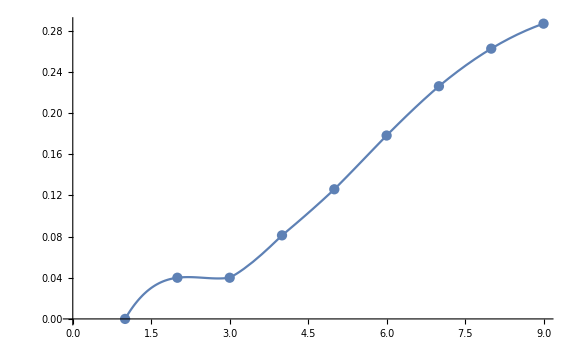

```mathematica
Show[ListPlot[list,ImageSize->Large],Plot[Interpolation[list][x],{x,1,9}]]
```

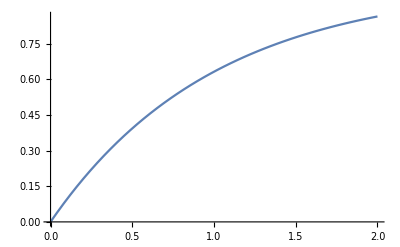

```mathematica
Plot[1-E^-x,{x,0,2}]
```

```mathematica
Clear[AA,Aa,aa];
AA[1]=0;
Aa[1]=0.4;
aa[1]=0.6;
AA[n_]:=(AA[n-1]^2+AA[n-1]*Aa[n-1]+1/4 Aa[n-1]^2)/(AA[n-1]+Aa[n-1]+aa[n-1])^2;
Aa[n_]:=Module[{},
(2*AA[n-1]*aa[n-1]+AA[n-1]*Aa[n-1]+1/2 Aa[n-1]^2)/(AA[n-1]+Aa[n-1]+aa[n-1])^2 ;



aa[n_]=(aa[n-1]^2+aa[n-1]*Aa[n-1]*Aa[n-1]+1/4 Aa[n-1]^2)/(AA[n-1]+Aa[n-1]+aa[n-1])^2;

Generation[n_]:=
```

```mathematica
Generation[n_]:=Module[{AA1,Aa1,aa1,AA2,Aa2,aa2},
{AA1,Aa1,aa1}=Generation[n-1];
AA2=(AA1^2+AA1*Aa1+1/4 Aa1^2)/(AA1+Aa1+aa1)^2 ;
Aa2=(2*AA1*aa1+AA1*Aa1+1/2 Aa1^2)/(AA1+Aa1+aa1)^2;
aa2=(2*aa1^2+aa1*Aa1+1/4 Aa1^2)/(AA1+Aa1+aa1)^2;
{AA2,(1-Aa2/(AA2+Aa2+aa2))Aa2,(1-aa2/(AA2+Aa2+aa2))aa2}
];
```

{0.246963,0.237491,0.232117}

```mathematica
Generation[1]={0,0.001,0.999};
Generation[n_]:=Module[{AA1,Aa1,aa1,AA2,Aa2,aa2},
{AA1,Aa1,aa1}=Generation[n-1];
AA2=(AA1^2+AA1*Aa1+1/4 Aa1^2)/(AA1+Aa1+aa1)^2 ;
Aa2=(2*AA1*aa1+AA1*Aa1+1/2 Aa1^2)/(AA1+Aa1+aa1)^2;
aa2=(2*aa1^2+aa1*Aa1+1/4 Aa1^2)/(AA1+Aa1+aa1)^2;
{AA2,4(1-(AA2+aa2)/(AA2+Aa2+aa2))Aa2,0.9(1-(AA2+aa2)/(AA2+Aa2+aa2))aa2}
];
```

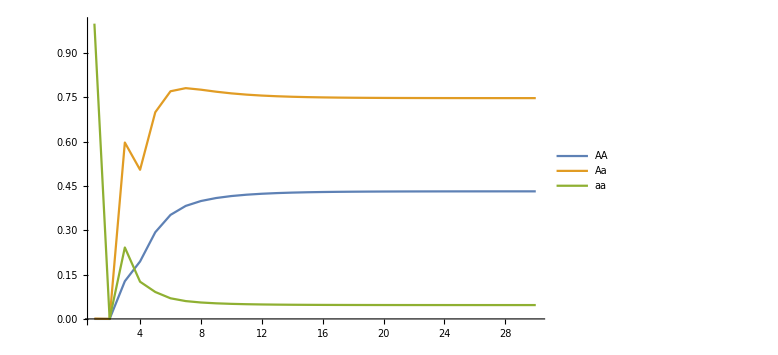

```mathematica
ListPlot[Transpose@(Table[{i,#}&/@Generation[i],{i,1,30}]),Joined->True,PlotLegends->{AA,Aa,aa},PlotRange->All,ImageSize->Large]
```

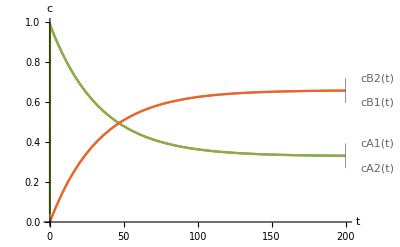

reactionk=2V=100.eps

```mathematica
ReactionPlot[k_,V_,range_]:=Module[{ka,kb,k1,k2,c,V1,V2,a},a=DSolve[{D[cA1[t],t]==-ka/V1*(cA1[t]-cA2[t]),
	D[cB1[t],t]==kb/V1*(cB2[t]-cB1[t]),
	D[cA2[t],t]==ka/V2*(cA1[t]-cA2[t])-k1*cA2[t]+k2*cB2[t],
	D[cB2[t],t]==-kb/V2*(cB2[t]-cB1[t])+k1*cA2[t]-k2*cB2[t],
	cA1[0]==c,cB1[0]==0,cA2[0]==0,cB2[0]==0}/.{ka->100,kb->100,k1->k,k2->1,c->1,V1->1,V2->1/V},
{cA1[t],cB1[t],cA2[t],cB2[t]},t];
Plot[Evaluate[{cA1[t],cB1[t],cA2[t],cB2[t]}/.a],{t,0,range},PlotLabels->{cA1[t],cB1[t],cA2[t],cB2[t]},ImageSize->Full,AxesLabel->{"t","c"},PlotRange->All]
];
ReactionPlot[2,100,200]
Export["reactionk=2V=100.eps",%]
```

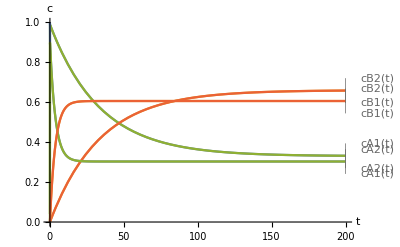

```mathematica
Show[ReactionPlot[2,100,200],ReactionPlot[2,10,200]]
```

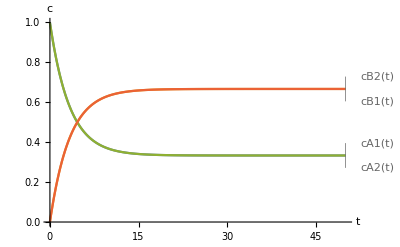

```mathematica
a=DSolve[{D[cA1[t],t]==-ka/V1*(cA1[t]-cA2[t]),
	D[cB1[t],t]==kb/V1*(cB2[t]-cB1[t]),
	D[cA2[t],t]==ka/V2*(cA1[t]-cA2[t])-k1*cA2[t]+k2*cB2[t],
	D[cB2[t],t]==-kb/V2*(cB2[t]-cB1[t])+k1*cA2[t]-k2*cB2[t],
	cA1[0]==c,cB1[0]==0,cA2[0]==0,cB2[0]==0}/.{ka->10000,kb->10000,k1->200,k2->100,c->1,V1->1,V2->1/1000},
{cA1[t],cB1[t],cA2[t],cB2[t]},t];
Plot[Evaluate[{cA1[t],cB1[t],cA2[t],cB2[t]}/.a],{t,0,50},PlotLabels->{cA1[t],cB1[t],cA2[t],cB2[t]},ImageSize->Full,AxesLabel->{"t","c"},PlotRange->All]
```

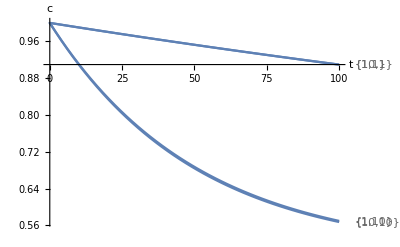

```mathematica
Module[{ka,kb,k1,k2,c,V1,V2,a},a=DSolve[{D[cA1[t],t]==-ka/V1*(cA1[t]-cA2[t]),
	D[cB1[t],t]==kb/V1*(cB2[t]-cB1[t]),
	D[cA2[t],t]==ka/V2*(cA1[t]-cA2[t])-k1*cA2[t]+k2*cB2[t],
	D[cB2[t],t]==-kb/V2*(cB2[t]-cB1[t])+k1*cA2[t]-k2*cB2[t],
	cA1[0]==c,cB1[0]==0,cA2[0]==0,cB2[0]==0}/.{ka->kl,kb->kl,k1->k,k2->k,c->1,V1->1,V2->1/V},
{cA1[t],cB1[t],cA2[t],cB2[t]},t];
Plot[Evaluate[cA1[t]/.a],{t,0,range},PlotLabels->HoldForm[Evaluate@{kl,k}],ImageSize->Full,AxesLabel->{"t","c"},PlotRange->All]
];
Show@@(ReactionPlot1[#1,#2,1000,100]&@@@Flatten[Table[{10^i,10^j},{i,0,1},{j,0,1}],1])
```

```mathematica
Flatten[Table[{10^i,10^j},{i,0,3},{j,0,3}],1]
```

{{1,1},{1,10},{1,100},{1,1000},{10,1},{10,10},{10,100},{10,1000},{100,1},{100,10},{100,100},{100,1000},{1000,1},{1000,10},{1000,100},{1000,1000}}

```mathematica
list=cA1[t]/.DSolve[{D[cA1[t],t]==-ka/V1*(cA1[t]-cA2[t]),
	D[cB1[t],t]==kb/V1*(cB2[t]-cB1[t]),
	D[cA2[t],t]==ka/V2*(cA1[t]-cA2[t])-k1*cA2[t]+k2*cB2[t],
	D[cB2[t],t]==-kb/V2*(cB2[t]-cB1[t])+k1*cA2[t]-k2*cB2[t],
	cA1[0]==c,cB1[0]==0,cA2[0]==0,cB2[0]==0}/.{ka->#1,kb->#1,k1->#2,k2->#2,c->1,V1->1,V2->1/V},
{cA1[t],cB1[t],cA2[t],cB2[t]},t]&@@@(Flatten[Table[{2^i,2^j},{i,0,10},{j,0,0}],1])/.V->1000;
Export["reactionkavariate.eps",Plot[list,{t,0,100},AxesLabel->{t,c}]]
```

reactionkavariate.eps

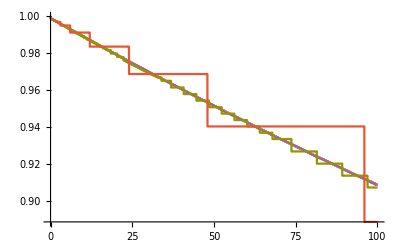

```mathematica
Plot[list,{t,0,100}]
```

```mathematica
list
```

{{(1000 (2012002000+2012002 ⅇ^(-1001 t)+1007007001 ⅇ^(1/2 (-1003-√1006001) t)-1002001 √1006001 ⅇ^(1/2 (-1003-√1006001) t)+1007007001 ⅇ^(1/2 (-1003+√1006001) t)+1002001 √1006001 ⅇ^(1/2 (-1003+√1006001) t)))/(1001 (1006001-1001 √1006001) (1006001+1001 √1006001))},{(1000 (2084722000+2084722 ⅇ^(-1001 t)+1043403361 ⅇ^(1/2 (-1021-√1042361) t)-1020019 √1042361 ⅇ^(1/2 (-1021-√1042361) t)+1043403361 ⅇ^(1/2 (-1021+√1042361) t)+1020019 √1042361 ⅇ^(1/2 (-1021+√1042361) t)))/(1001 (1042361-1019 √1042361) (1042361+1019 √1042361))},{(1000 (2883202000+2883202 ⅇ^(-1001 t)+1443042601 ⅇ^(1/2 (-1201-√1441601) t)-1200199 √1441601 ⅇ^(1/2 (-1201-√1441601) t)+1443042601 ⅇ^(1/2 (-1201+√1441601) t)+1200199 √1441601 ⅇ^(1/2 (-1201+√1441601) t)))/(1001 (1441601-1199 √1441601) (1441601+1199 √1441601))},{(1000 (17996002000+17996002 ⅇ^(-1001 t)+9006999001 ⅇ^(1/2 (-3001-√8998001) t)-3001999 √8998001 ⅇ^(1/2 (-3001-√8998001) t)+9006999001 ⅇ^(1/2 (-3001+√8998001) t)+3001999 √8998001 ⅇ^(1/2 (-3001+√8998001) t)))/(1001 (8998001-2999 √8998001) (8998001+2999 √8998001))},{(25 ⅇ^(-10010 t) (50120032000+50120032000000 ⅇ^(10010 t)+25085076016000 ⅇ^(10010 t+(-5006-4 √1566251) t)-20003984000 √1566251 ⅇ^(10010 t+(-5006-4 √1566251) t)+25085076016000 ⅇ^(10010 t+(-5006+4 √1566251) t)+20003984000 √1566251 ⅇ^(10010 t+(-5006+4 √1566251) t)))/(1001 (25060016-19984 √1566251) (25060016+19984 √1566251))},{(1000 (2012002000+2012002 ⅇ^(-10010 t)+1007007001 ⅇ^(5 (-1003-√1006001) t)-1002001 √1006001 ⅇ^(5 (-1003-√1006001) t)+1007007001 ⅇ^(5 (-1003+√1006001) t)+1002001 √1006001 ⅇ^(5 (-1003+√1006001) t)))/(1001 (1006001-1001 √1006001) (1006001+1001 √1006001))},{(1000 (2084722000+2084722 ⅇ^(-10010 t)+1043403361 ⅇ^(5 (-1021-√1042361) t)-1020019 √1042361 ⅇ^(5 (-1021-√1042361) t)+1043403361 ⅇ^(5 (-1021+√1042361) t)+1020019 √1042361 ⅇ^(5 (-1021+√1042361) t)))/(1001 (1042361-1019 √1042361) (1042361+1019 √1042361))},{(1000 (2883202000+2883202 ⅇ^(-10010 t)+1443042601 ⅇ^(5 (-1201-√1441601) t)-1200199 √1441601 ⅇ^(5 (-1201-√1441601) t)+1443042601 ⅇ^(5 (-1201+√1441601) t)+1200199 √1441601 ⅇ^(5 (-1201+√1441601) t)))/(1001 (1441601-1199 √1441601) (1441601+1199 √1441601))},{(2500 ⅇ^(-100100 t) (5010204802000+5010204802000000 ⅇ^(100100 t)+2507607503401000 ⅇ^(100100 t+(-50051-√2505102401) t)-50000951000 √2505102401 ⅇ^(100100 t+(-50051-√2505102401) t)+2507607503401000 ⅇ^(100100 t+(-50051+√2505102401) t)+50000951000 √2505102401 ⅇ^(100100 t+(-50051+√2505102401) t)))/(1001 (2505102401-49951 √2505102401) (2505102401+49951 √2505102401))},{(25 ⅇ^(-100100 t) (50120032000+50120032000000 ⅇ^(100100 t)+25085076016000 ⅇ^(100100 t+10 (-5006-4 √1566251) t)-20003984000 √1566251 ⅇ^(100100 t+10 (-5006-4 √1566251) t)+25085076016000 ⅇ^(100100 t+10 (-5006+4 √1566251) t)+20003984000 √1566251 ⅇ^(100100 t+10 (-5006+4 √1566251) t)))/(1001 (25060016-19984 √1566251) (25060016+19984 √1566251))},{(1000 (2012002000+2012002 ⅇ^(-100100 t)+1007007001 ⅇ^(50 (-1003-√1006001) t)-1002001 √1006001 ⅇ^(50 (-1003-√1006001) t)+1007007001 ⅇ^(50 (-1003+√1006001) t)+1002001 √1006001 ⅇ^(50 (-1003+√1006001) t)))/(1001 (1006001-1001 √1006001) (1006001+1001 √1006001))},{(1000 (2084722000+2084722 ⅇ^(-100100 t)+1043403361 ⅇ^(50 (-1021-√1042361) t)-1020019 √1042361 ⅇ^(50 (-1021-√1042361) t)+1043403361 ⅇ^(50 (-1021+√1042361) t)+1020019 √1042361 ⅇ^(50 (-1021+√1042361) t)))/(1001 (1042361-1019 √1042361) (1042361+1019 √1042361))},{(250000 ⅇ^(-1001000 t) (501002498002000+501002498002000000 ⅇ^(1001000 t)+250751750250001000 ⅇ^(1001000 t+(-500501-√250501249001) t)-500000501000 √250501249001 ⅇ^(1001000 t+(-500501-√250501249001) t)+250751750250001000 ⅇ^(1001000 t+(-500501+√250501249001) t)+500000501000 √250501249001 ⅇ^(1001000 t+(-500501+√250501249001) t)))/(1001 (250501249001-499501 √250501249001) (250501249001+499501 √250501249001))},{(2500 ⅇ^(-1001000 t) (5010204802000+5010204802000000 ⅇ^(1001000 t)+2507607503401000 ⅇ^(1001000 t+10 (-50051-√2505102401) t)-50000951000 √2505102401 ⅇ^(1001000 t+10 (-50051-√2505102401) t)+2507607503401000 ⅇ^(1001000 t+10 (-50051+√2505102401) t)+50000951000 √2505102401 ⅇ^(1001000 t+10 (-50051+√2505102401) t)))/(1001 (2505102401-49951 √2505102401) (2505102401+49951 √2505102401))},{(25 ⅇ^(-1001000 t) (50120032000+50120032000000 ⅇ^(1001000 t)+25085076016000 ⅇ^(1001000 t+100 (-5006-4 √1566251) t)-20003984000 √1566251 ⅇ^(1001000 t+100 (-5006-4 √1566251) t)+25085076016000 ⅇ^(1001000 t+100 (-5006+4 √1566251) t)+20003984000 √1566251 ⅇ^(1001000 t+100 (-5006+4 √1566251) t)))/(1001 (25060016-19984 √1566251) (25060016+19984 √1566251))},{(1000 (2012002000+2012002 ⅇ^(-1001000 t)+1007007001 ⅇ^(500 (-1003-√1006001) t)-1002001 √1006001 ⅇ^(500 (-1003-√1006001) t)+1007007001 ⅇ^(500 (-1003+√1006001) t)+1002001 √1006001 ⅇ^(500 (-1003+√1006001) t)))/(1001 (1006001-1001 √1006001) (1006001+1001 √1006001))}}

```mathematica
HoldForm/@(Flatten[Table[{10^i,10^j},{i,0,3},{j,0,3}],1])
```

{{1,1},{1,10},{1,100},{1,1000},{10,1},{10,10},{10,100},{10,1000},{100,1},{100,10},{100,100},{100,1000},{1000,1},{1000,10},{1000,100},{1000,1000}}

```mathematica
Flatten@list
```

{(1000 (2012002000+2012002 ⅇ^(-1001 t)+1007007001 ⅇ^(1/2 (-1003-√1006001) t)-1002001 √1006001 ⅇ^(1/2 (-1003-√1006001) t)+1007007001 ⅇ^(1/2 (-1003+√1006001) t)+1002001 √1006001 ⅇ^(1/2 (-1003+√1006001) t)))/(1001 (1006001-1001 √1006001) (1006001+1001 √1006001)),(1000 (2084722000+2084722 ⅇ^(-1001 t)+1043403361 ⅇ^(1/2 (-1021-√1042361) t)-1020019 √1042361 ⅇ^(1/2 (-1021-√1042361) t)+1043403361 ⅇ^(1/2 (-1021+√1042361) t)+1020019 √1042361 ⅇ^(1/2 (-1021+√1042361) t)))/(1001 (1042361-1019 √1042361) (1042361+1019 √1042361)),(1000 (2883202000+2883202 ⅇ^(-1001 t)+1443042601 ⅇ^(1/2 (-1201-√1441601) t)-1200199 √1441601 ⅇ^(1/2 (-1201-√1441601) t)+1443042601 ⅇ^(1/2 (-1201+√1441601) t)+1200199 √1441601 ⅇ^(1/2 (-1201+√1441601) t)))/(1001 (1441601-1199 √1441601) (1441601+1199 √1441601)),(1000 (17996002000+17996002 ⅇ^(-1001 t)+9006999001 ⅇ^(1/2 (-3001-√8998001) t)-3001999 √8998001 ⅇ^(1/2 (-3001-√8998001) t)+9006999001 ⅇ^(1/2 (-3001+√8998001) t)+3001999 √8998001 ⅇ^(1/2 (-3001+√8998001) t)))/(1001 (8998001-2999 √8998001) (8998001+2999 √8998001)),(25 ⅇ^(-10010 t) (50120032000+50120032000000 ⅇ^(10010 t)+25085076016000 ⅇ^(10010 t+(-5006-4 √1566251) t)-20003984000 √1566251 ⅇ^(10010 t+(-5006-4 √1566251) t)+25085076016000 ⅇ^(10010 t+(-5006+4 √1566251) t)+20003984000 √1566251 ⅇ^(10010 t+(-5006+4 √1566251) t)))/(1001 (25060016-19984 √1566251) (25060016+19984 √1566251)),(1000 (2012002000+2012002 ⅇ^(-10010 t)+1007007001 ⅇ^(5 (-1003-√1006001) t)-1002001 √1006001 ⅇ^(5 (-1003-√1006001) t)+1007007001 ⅇ^(5 (-1003+√1006001) t)+1002001 √1006001 ⅇ^(5 (-1003+√1006001) t)))/(1001 (1006001-1001 √1006001) (1006001+1001 √1006001)),(1000 (2084722000+2084722 ⅇ^(-10010 t)+1043403361 ⅇ^(5 (-1021-√1042361) t)-1020019 √1042361 ⅇ^(5 (-1021-√1042361) t)+1043403361 ⅇ^(5 (-1021+√1042361) t)+1020019 √1042361 ⅇ^(5 (-1021+√1042361) t)))/(1001 (1042361-1019 √1042361) (1042361+1019 √1042361)),(1000 (2883202000+2883202 ⅇ^(-10010 t)+1443042601 ⅇ^(5 (-1201-√1441601) t)-1200199 √1441601 ⅇ^(5 (-1201-√1441601) t)+1443042601 ⅇ^(5 (-1201+√1441601) t)+1200199 √1441601 ⅇ^(5 (-1201+√1441601) t)))/(1001 (1441601-1199 √1441601) (1441601+1199 √1441601)),(2500 ⅇ^(-100100 t) (5010204802000+5010204802000000 ⅇ^(100100 t)+2507607503401000 ⅇ^(100100 t+(-50051-√2505102401) t)-50000951000 √2505102401 ⅇ^(100100 t+(-50051-√2505102401) t)+2507607503401000 ⅇ^(100100 t+(-50051+√2505102401) t)+50000951000 √2505102401 ⅇ^(100100 t+(-50051+√2505102401) t)))/(1001 (2505102401-49951 √2505102401) (2505102401+49951 √2505102401)),(25 ⅇ^(-100100 t) (50120032000+50120032000000 ⅇ^(100100 t)+25085076016000 ⅇ^(100100 t+10 (-5006-4 √1566251) t)-20003984000 √1566251 ⅇ^(100100 t+10 (-5006-4 √1566251) t)+25085076016000 ⅇ^(100100 t+10 (-5006+4 √1566251) t)+20003984000 √1566251 ⅇ^(100100 t+10 (-5006+4 √1566251) t)))/(1001 (25060016-19984 √1566251) (25060016+19984 √1566251)),(1000 (2012002000+2012002 ⅇ^(-100100 t)+1007007001 ⅇ^(50 (-1003-√1006001) t)-1002001 √1006001 ⅇ^(50 (-1003-√1006001) t)+1007007001 ⅇ^(50 (-1003+√1006001) t)+1002001 √1006001 ⅇ^(50 (-1003+√1006001) t)))/(1001 (1006001-1001 √1006001) (1006001+1001 √1006001)),(1000 (2084722000+2084722 ⅇ^(-100100 t)+1043403361 ⅇ^(50 (-1021-√1042361) t)-1020019 √1042361 ⅇ^(50 (-1021-√1042361) t)+1043403361 ⅇ^(50 (-1021+√1042361) t)+1020019 √1042361 ⅇ^(50 (-1021+√1042361) t)))/(1001 (1042361-1019 √1042361) (1042361+1019 √1042361)),(250000 ⅇ^(-1001000 t) (501002498002000+501002498002000000 ⅇ^(1001000 t)+250751750250001000 ⅇ^(1001000 t+(-500501-√250501249001) t)-500000501000 √250501249001 ⅇ^(1001000 t+(-500501-√250501249001) t)+250751750250001000 ⅇ^(1001000 t+(-500501+√250501249001) t)+500000501000 √250501249001 ⅇ^(1001000 t+(-500501+√250501249001) t)))/(1001 (250501249001-499501 √250501249001) (250501249001+499501 √250501249001)),(2500 ⅇ^(-1001000 t) (5010204802000+5010204802000000 ⅇ^(1001000 t)+2507607503401000 ⅇ^(1001000 t+10 (-50051-√2505102401) t)-50000951000 √2505102401 ⅇ^(1001000 t+10 (-50051-√2505102401) t)+2507607503401000 ⅇ^(1001000 t+10 (-50051+√2505102401) t)+50000951000 √2505102401 ⅇ^(1001000 t+10 (-50051+√2505102401) t)))/(1001 (2505102401-49951 √2505102401) (2505102401+49951 √2505102401)),(25 ⅇ^(-1001000 t) (50120032000+50120032000000 ⅇ^(1001000 t)+25085076016000 ⅇ^(1001000 t+100 (-5006-4 √1566251) t)-20003984000 √1566251 ⅇ^(1001000 t+100 (-5006-4 √1566251) t)+25085076016000 ⅇ^(1001000 t+100 (-5006+4 √1566251) t)+20003984000 √1566251 ⅇ^(1001000 t+100 (-5006+4 √1566251) t)))/(1001 (25060016-19984 √1566251) (25060016+19984 √1566251)),(1000 (2012002000+2012002 ⅇ^(-1001000 t)+1007007001 ⅇ^(500 (-1003-√1006001) t)-1002001 √1006001 ⅇ^(500 (-1003-√1006001) t)+1007007001 ⅇ^(500 (-1003+√1006001) t)+1002001 √1006001 ⅇ^(500 (-1003+√1006001) t)))/(1001 (1006001-1001 √1006001) (1006001+1001 √1006001))}

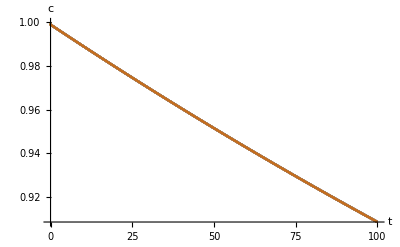

Export::noopen: Cannot open reactionka.eps.

$Failed

```mathematica
list=cA1[t]/.DSolve[{D[cA1[t],t]==-ka/V1*(cA1[t]-cA2[t]),
	D[cB1[t],t]==kb/V1*(cB2[t]-cB1[t]),
	D[cA2[t],t]==ka/V2*(cA1[t]-cA2[t])-k1*cA2[t]+k2*cB2[t],
	D[cB2[t],t]==-kb/V2*(cB2[t]-cB1[t])+k1*cA2[t]-k2*cB2[t],
	cA1[0]==c,cB1[0]==0,cA2[0]==0,cB2[0]==0}/.{ka->#1,kb->#1,k1->#2,k2->#2,c->1,V1->1,V2->1/V},
{cA1[t],cB1[t],cA2[t],cB2[t]},t]&@@@(Flatten[Table[{2^i,2^j},{i,0,20},{j,0,0}],1])/.V->1000;
Plot[list,{t,0,100},AxesLabel->{t,c}]
Export["reactionka.eps",%]
```

```mathematica
NDSolve[{D[cA1[t],t]==-ka/V1*If[cA1[t]>=cA2[t],cA1[t]-cA2[t],0],
	D[cB1[t],t]==kb/V1*If[cB2[t]>=cB1[t],cB2[t]-cB1[t],0],
	D[cA2[t],t]==ka/V2*If[cA1[t]>=cA2[t],cA1[t]-cA2[t],0]-k1*cA2[t]+k2*cB2[t],
	D[cB2[t],t]==-kb/V2*If[cB2[t]>=cB1[t],cB2[t]-cB1[t],0]+k1*cA2[t]-k2*cB2[t],
	cA1[0]==0,cB1[0]==c,cA2[0]==0,cB2[0]==0}/.{ka->10,kb->10,k1->1,k2->1,c->1,V1->1,V2->0.001},
{cA1[t],cB1[t],cA2[t],cB2[t]},{t,0,1000}];
Export["antireaction.eps",Plot[Evaluate[{cA1[t],cB1[t],cA2[t],cB2[t]}/.%],{t,0,1000},AxesLabel->{t,c},PlotLabels->{cA1[t],cB1[t],cA2[t],cB2[t]},ImageSize->Large]]
```

antireaction.eps

```mathematica
HoldForm[MatrixForm@{{(-Subscript[k, A])/Subscript[V, 1],Subscript[k, A]/Subscript[V, 1],0,0},{Subscript[k, A]/Subscript[V, 2],-Subscript[k, A]/Subscript[V, 2]-Subscript[k, 1],Subscript[k, 2],0},{0,Subscript[k, 1],-Subscript[k, 2]-Subscript[k, B]/Subscript[V, 2],Subscript[k, B]/Subscript[V, 2]},{0,0,Subscript[k, B]/Subscript[V, 1],-Subscript[k, B]/Subscript[V, 1]}}.Evaluate[MatrixForm@Transpose[{{Subscript[c, A,1],Subscript[c, A,2],Subscript[c, B,1],Subscript[c, B,2]}}]]]
```

(-k_A/V_1 | k_A/V_1 | 0 | 0
k_A/V_2 | -k_A/V_2-k_1 | k_2 | 0
0 | k_1 | -k_2-k_B/V_2 | k_B/V_2
0 | 0 | k_B/V_1 | -k_B/V_1).Evaluate[Transpose[{{c_(A,1),c_(A,2),c_(B,1),c_(B,2)}}]]

```mathematica
Transpose[{{Subscript[c, A,1],Subscript[c, A,2],Subscript[c, B,1],Subscript[c, B,2]}}]
```

{{c_(A,1)},{c_(A,2)},{c_(B,1)},{c_(B,2)}}

```mathematica
MatrixForm@Transpose[{{Subscript[c, A,1],Subscript[c, A,2],Subscript[c, B,1],Subscript[c, B,2]}}]
```

(c_(A,1)
c_(A,2)
c_(B,1)
c_(B,2))

```mathematica
a=MatrixForm@{{(-Subscript[k, A])/Subscript[V, 1],Subscript[k, A]/Subscript[V, 1],0,0},{Subscript[k, A]/Subscript[V, 2],-Subscript[k, A]/Subscript[V, 2]-Subscript[k, 1],Subscript[k, 2],0},{0,Subscript[k, 1],-Subscript[k, 2]-Subscript[k, B]/Subscript[V, 2],Subscript[k, B]/Subscript[V, 2]},{0,0,Subscript[k, B]/Subscript[V, 1],-Subscript[k, B]/Subscript[V, 1]}};
b=MatrixForm@Transpose[{{Subscript[c, A,1],Subscript[c, A,2],Subscript[c, B,1],Subscript[c, B,2]}}]
```

```mathematica
HoldForm[({{-Subscript[k, A]/Subscript[V, 1], Subscript[k, A]/Subscript[V, 1], 0, 0}, {Subscript[k, A]/Subscript[V, 2], -Subscript[k, A]/Subscript[V, 2]-Subscript[k, 1], Subscript[k, 2], 0}, {0, Subscript[k, 1], -Subscript[k, 2]-Subscript[k, B]/Subscript[V, 2], Subscript[k, B]/Subscript[V, 2]}, {0, 0, Subscript[k, B]/Subscript[V, 1], -Subscript[k, B]/Subscript[V, 1]}})({{Subscript[c, A,1]}, {Subscript[c, A,2]}, {Subscript[c, B,1]}, {Subscript[c, B,2]}})=d/dt({{Subscript[c, A,1]}, {Subscript[c, A,2]}, {Subscript[c, B,1]}, {Subscript[c, B,2]}})]
```

{{-k_A/V_1,k_A/V_1,0,0},{k_A/V_2,-k_A/V_2-k_1,k_2,0},{0,k_1,-k_2-k_B/V_2,k_B/V_2},{0,0,k_B/V_1,-k_B/V_1}} {{c_(A,1)},{c_(A,2)},{c_(B,1)},{c_(B,2)}}=(d {{c_(A,1)},{c_(A,2)},{c_(B,1)},{c_(B,2)}})/dt

```mathematica
Hold[a.b]
```

```mathematica
Hold[({{-Subscript[k, A]/Subscript[V, 1], Subscript[k, A]/Subscript[V, 1], 0, 0}, {Subscript[k, A]/Subscript[V, 2], -Subscript[k, A]/Subscript[V, 2]-Subscript[k, 1], Subscript[k, 2], 0}, {0, Subscript[k, 1], -Subscript[k, 2]-Subscript[k, B]/Subscript[V, 2], Subscript[k, B]/Subscript[V, 2]}, {0, 0, Subscript[k, B]/Subscript[V, 1], -Subscript[k, B]/Subscript[V, 1]}})({{Subscript[c, A,1]}, {Subscript[c, A,2]}, {Subscript[c, B,1]}, {Subscript[c, B,2]}})=d/dt({{Subscript[c, A,1]}, {Subscript[c, A,2]}, {Subscript[c, B,1]}, {Subscript[c, B,2]}})]
```

Syntax::bktmop: Expression "Hold[(-k_A/V_1 | k_A/V_1 | 0 | 0
k_A/V_2 | -k_A/V_2-k_1 | k_2 | 0
0 | k_1 | -k_2-k_B/V_2 | k_B/V_2
0 | 0 | k_B/V_1 | -k_B/V_1)(c_(A,1)
c_(A,2)
c_(B,1)
c_(B,2))=d/dt(c_(A,1)
c_(A,2)
c_(B,1)
c_(B,2))]" has no opening "[".

```mathematica
({{-Subscript[k, A]/Subscript[V, 1], Subscript[k, A]/Subscript[V, 1], 0, 0}, {Subscript[k, A]/Subscript[V, 2], -Subscript[k, A]/Subscript[V, 2]-Subscript[k, 1], Subscript[k, 2], 0}, {0, Subscript[k, 1], -Subscript[k, 2]-Subscript[k, B]/Subscript[V, 2], Subscript[k, B]/Subscript[V, 2]}, {0, 0, Subscript[k, B]/Subscript[V, 1], -Subscript[k, B]/Subscript[V, 1]}})({{Subscript[c, A,1]}, {Subscript[c, A,2]}, {Subscript[c, B,1]}, {Subscript[c, B,2]}})=d/dt({{Subscript[c, A,1]}, {Subscript[c, A,2]}, {Subscript[c, B,1]}, {Subscript[c, B,2]}})
```

Set::write: Tag Times in {{c_(A,1)},{c_(A,2)},{c_(B,1)},{c_(B,2)}} {{-k_A/V_1,k_A/V_1,0,0},{k_A/V_2,-k_1-k_A/V_2,k_2,0},{0,k_1,-k_2-k_B/V_2,k_B/V_2},{0,0,k_B/V_1,-k_B/V_1}} is Protected.

{{(d c_(A,1))/dt},{(d c_(A,2))/dt},{(d c_(B,1))/dt},{(d c_(B,2))/dt}}

```mathematica
({{-Subscript[k, A]/Subscript[V, 1], Subscript[k, A]/Subscript[V, 1], 0, 0}, {Subscript[k, A]/Subscript[V, 2], -Subscript[k, A]/Subscript[V, 2]-Subscript[k, 1], Subscript[k, 2], 0}, {0, Subscript[k, 1], -Subscript[k, 2]-Subscript[k, B]/Subscript[V, 2], Subscript[k, B]/Subscript[V, 2]}, {0, 0, Subscript[k, B]/Subscript[V, 1], -Subscript[k, B]/Subscript[V, 1]}})({{Subscript[c, A,1]}, {Subscript[c, A,2]}, {Subscript[c, B,1]}, {Subscript[c, B,2]}})=d/dt({{Subscript[c, A,1]}, {Subscript[c, A,2]}, {Subscript[c, B,1]}, {Subscript[c, B,2]}})
```

Set::write: Tag Times in {{c_(A,1)},{c_(A,2)},{c_(B,1)},{c_(B,2)}} {{-k_A/V_1,k_A/V_1,0,0},{k_A/V_2,-k_1-k_A/V_2,k_2,0},{0,k_1,-k_2-k_B/V_2,k_B/V_2},{0,0,k_B/V_1,-k_B/V_1}} is Protected.

{{(d c_(A,1))/dt},{(d c_(A,2))/dt},{(d c_(B,1))/dt},{(d c_(B,2))/dt}}

```mathematica
TeXForm[-Subscript[k, A]/Subscript[V, 1]]
```

-\frac{k_A}{V_1}

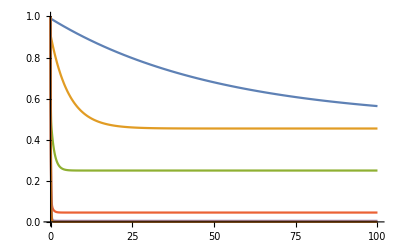

```mathematica
list=cA1[t]/.DSolve[{D[cA1[t],t]==-ka/V1*(cA1[t]-cA2[t]),
	D[cB1[t],t]==kb/V1*(cB2[t]-cB1[t]),
	D[cA2[t],t]==ka/V2*(cA1[t]-cA2[t])-k1*cA2[t]+k2*cB2[t],
	D[cB2[t],t]==-kb/V2*(cB2[t]-cB1[t])+k1*cA2[t]-k2*cB2[t],
	cA1[0]==c,cB1[0]==0,cA2[0]==0,cB2[0]==0}/.{ka->10,kb->10,k1->1,k2->1,c->1,V1->1,V2->1/#},
{cA1[t],cB1[t],cA2[t],cB2[t]},t]&/@{100,10,1,0.1,0.01,0.001};
Plot[list,{t,0,100}]
```